-Graphics-

Bienvenidos a mmAeScience!
https://github.com/josemramirez/mmaescience/calc_intro -[for MMaTeX]_beta^v14

# eScience - Trabajar con Límites (2).

◀ prev - + prox ▶

e Guardar
d Resetear

### Visión general

Encontrar límites con una tabla puede ser un trabajo tedioso. Con las leyes de límites, puedes hacer esto mucho más fácilmente.

```mathematica
Esta lección repasará las leyes de los límites y usará las funciones de ejemplo f y g para ilustrarlas:
```

```mathematica
f[x_] := 2 x + 2
```

```mathematica
g[x_] := 3 Cos[x]/2
```

```mathematica
Estos son sus plots:
```

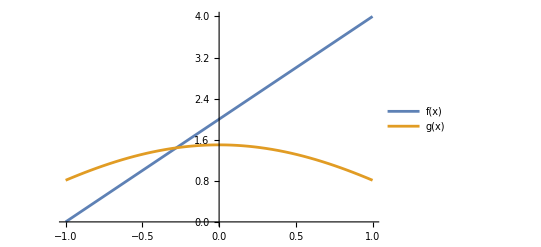

```mathematica
Plot[{f[x], g[x]}, {x, -1, 1}, PlotLegends -> "Expressions"]
```

Mejorado...

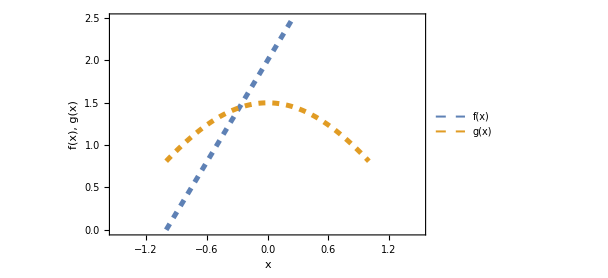

```mathematica
Plot[{f[x], g[x]}, {x, -1, 1}, PlotLegends -> "Expressions",Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,19],
PlotRange->{{-1.5,1.5},{-0.01,2.5}},
PlotStyle->{
{Thickness@0.008,Dashed}},
FrameLabel->{Style["x",24],Style["f(x),  g(x)",24]},
ImageSize->450]
```

```mathematica
Sus límites en 0 son 2 y 3/2, respectivamente:
```

```mathematica
Limit[f[x], x -> 0]
```

2

```mathematica
Limit[g[x], x -> 0]
```

3/2

◀ prev - + prox ▶

e Guardar
d Resetear

### Ley de la suma

```mathematica
El límite de una suma es la suma de los límites. Por lo tanto, el límite para f[x]+g[x] cuando x tiende a 0 es 
2+3/2 = 7/2.
```

```mathematica
Limit está de acuerdo:
```

```mathematica
Limit[f[x] + g[x], x -> 0]
```

7/2

A continuación se muestra un gráfico de las tres funciones:

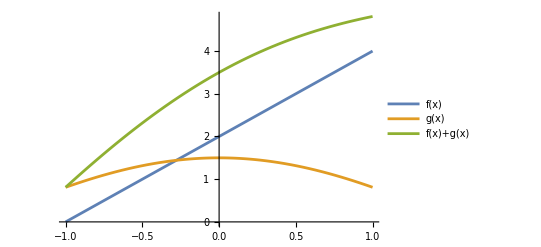

```mathematica
Plot[{f[x], g[x], f[x] + g[x]}, {x, -1, 1}, PlotLegends -> "Expressions"]
```

```mathematica
De la ley de la suma siguen la ley de la diferencia y la ley de la multiplicación escalar.
```

Ley de la diferencia: El límite de una diferencia es la diferencia de los límites.

```mathematica
Ley de multiplicación escalar: El límite de una constante multiplicada por una función es la constante multiplicada por el límite de la función.
```

El límite para f[x]-g[x] cuando x tiende a 0 es (2 - 3/2) = 1/2, y el límite para 3f[x] cuando x tiende a 0 es (3 x 2) = 6:

```mathematica
{Limit[f[x] - g[x], x -> 0], Limit[3 f[x], x -> 0]}
```

{1/2,6}

◀ prev - + prox ▶

e Guardar
d Resetear

### Ley del producto

```mathematica
El límite de un producto es el producto de los límites. Por lo tanto, el límite para f[x]*g[x] cuando x tiende a 0 es  
2 x 3/2 = 3.
```

```mathematica
Limit está de acuerdo:
```

```mathematica
Limit[f[x] g[x], x -> 0]
```

3

A continuación se muestra un gráfico de las tres funciones:

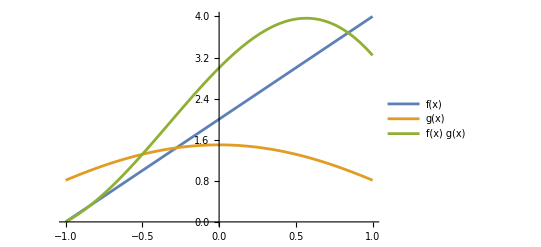

```mathematica
Plot[{f[x], g[x], f[x] g[x]}, {x, -1, 1}, PlotLegends -> "Expressions"]
```

La ley del producto se extiende naturalmente a una función de potencia.

```mathematica
Ley de potencias: El límite de una potencia de una función es la potencia del límite de la función.
```

```mathematica
El límite de f[x]^3 cuando x tiende a 0 es 2^3 = 8:
```

```mathematica
Limit[f[x]^3 , x -> 0]
```

8

◀ prev - + prox ▶

e Guardar
d Resetear

### Ley del cociente

```mathematica
El límite de un cociente es el cociente de los límites, siempre y cuando el límite del denominador no sea 0. Por lo tanto, el límite de f[x]/g[x] cuando x tiende a 0 es 2/(3/2) = 4/3.
```

Limit está de acuerdo:

```mathematica
Limit[f[x]/g[x], x -> 0]
```

4/3

```mathematica
A continuación se muestra un gráfico de las tres funciones:
```

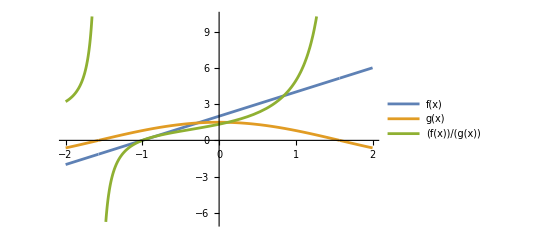

```mathematica
Plot[{f[x], g[x], f[x]/g[x]},{x, -2, 2}, PlotLegends -> "Expressions"]
```

```mathematica
Obsérvese que f/g no puede tener su límite calculado en π/2 con la ley del cociente porque g es 0 allí:
```

```mathematica
g[π/2]
```

0

```mathematica
Limit[f[x]/g[π/2], x -> π/2]
```

Indeterminate

◀ prev - + prox ▶

e Guardar
d Resetear

### Límite de un polinomio

```mathematica
El límite de un polinomio se puede calcular si se aceptan algunas cosas.
```

Primero, acepta que el límite de una función constante f[x]=c cuando x se aproxima a cualquier valor es la constante c:

```mathematica
Limit[c, x -> a] == c
```

True

```mathematica
Acepte también que el límite de la función g[x] = x en cualquier valor a es simplemente a:
```

```mathematica
Limit[x, x -> a] == a
```

True

Dado que los polinomios se pueden construir tomando g y multiplicándolo por sí mismo, así como sumando y multiplicando varias funciones constantes f, el límite de cualquier polinomio en cualquier punto a se calcula mediante la ley de la suma y la ley del producto como el valor del polinomio en a.

El límite del polinomio f[x]=2 x^2-4x+3 cuando x tiende a 4 es 2(4)^2-4(4)+3=19.

Limit está de acuerdo:

```mathematica
Limit[2 x^2  - 4 x + 3, x -> 4]
```

19

◀ prev - + prox ▶

e Guardar
d Resetear

### Límite de una función racional

Calcule el límite de la siguiente función cuando x tiende a −2:

```mathematica
f[x_] :=( x^3  - x^2  + 2) /( 5 x - 3)
```

```mathematica
Una función racional es una relación de dos funciones polinómicas. Dado que tienes la ley del cociente y sabes cómo calcular los límites de los polinomios, esto es bastante fácil.
```

Sus polinomios constituyentes son g[x]=x^3-x^2+2 y h[x]=5x-3:

```mathematica
g[x_] := x^3  - x ^2 + 2
```

```mathematica
h[x_] := -3 + 5 x
```

```mathematica
f[x] == g[x]/ h[x]
```

True

Limit muestra que se obtiene el mismo límite si se dividen los límites de los polinomios:

```mathematica
{Limit[ g[x]/ h[x] , x -> -2],Limit[ g[x]/ h[x] , x -> -2] == f[-2]}
```

{10/13,True}

Aquí están sus tramas; Se superponen porque son lo mismo:

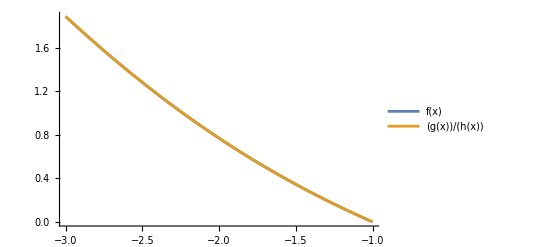

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[{f[x], g[x]/h[x]}, {x, -3, -1}, PlotLegends -> "Expressions"]
```

### Límite de una función racional: ejemplo especial

```mathematica
Calcule el límite de la siguiente función cuando x tiende a −1.
```

```mathematica
f[x_] := (x^2  - 1)/( x + 1)
```

```mathematica
El denominador es igual a 0 en −1, por lo que no se puede usar la ley del cociente:
```

```mathematica
x + 1 /. x -> -1
```

0

```mathematica
Para encontrar el límite, factoriza el numerador y ve si tiene un factor que cancele el denominador. Factor de uso:
```

```mathematica
Factor[x^2  - 1]
```

(-1+x) (1+x)

```mathematica
Puede ver que también aparece un (x+1) en el numerador, por lo que simplificar la expresión dará (x-1). Utilice Simplify:
```

```mathematica
Simplify[f[x]]
```

-1+x

Por lo tanto, el límite es −2, y puedes verlo en la gráfica de f:

```mathematica
Limit[f[x], x -> -1]
```

-2

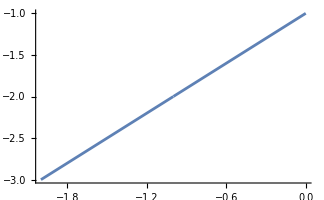

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, -2, 0}]
```

### Cociente de diferencia

Encuentre el límite para la siguiente función cuando h tiende a 0:

```mathematica
f[h_] :=((2 + h)^2-4)/h
```

```mathematica
Grafique la función:
```

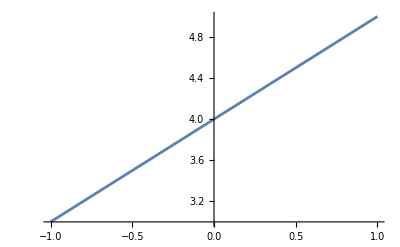

```mathematica
Plot[f[h], {h, -1, 1}]
```

Expande el numerador y observa si hay algo que se cancele con el denominador. Utilice Expand:

```mathematica
Expand[(2 + h)^2  - 4]
```

4 h+h^2

Dado que h también es un factor del denominador, cancélelo:

```mathematica
Factor[f[h]]
```

4+h

Ahora está claro que el límite cuando h se acerca a 0 debe ser 4.

Confirmar con límite:

```mathematica
Limit[f[h], h -> 0]
```

4

◀ prev - + prox ▶

e Guardar
d Resetear

### Límites unilaterales: función de valor absoluto

```mathematica
A veces, encontrar los límites izquierdo y derecho de una función es la forma más fácil de encontrar el límite general. Recuerde que el límite de una función existe si y solo si los límites izquierdo y derecho existen y son iguales.
```

Calcule el límite para la función de valor absoluto |x| A medida que x tiende a 0:

```mathematica
f[x_] := RealAbs[x]
```

Comience trazando la función:

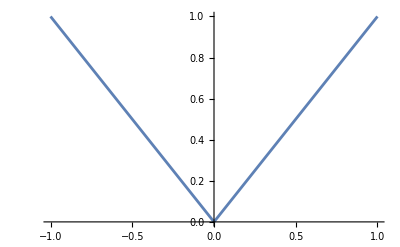

```mathematica
Plot[f[x], {x, -1, 1}]
```

Mejorado

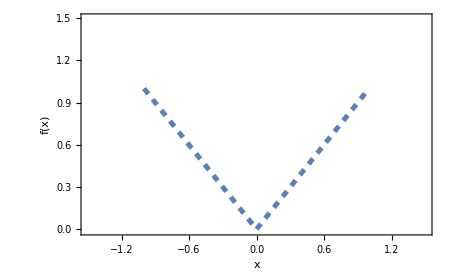

```mathematica
Plot[f[x], {x, -1, 1},
Frame->True,
FrameStyle->Directive[FontFamily->"Times"],
LabelStyle->Directive[Black,21],
PlotRange->{{-1.5,1.5},{-0.01,1.5}},
PlotStyle->{
{Thickness@0.008,Dashed}},
FrameLabel->{Style["x",24],Style["f(x)",24]},
ImageSize->450]
```

Está claro que el límite de la izquierda y el límite de la derecha son de 0 a 0.

Ahora confirme esta respuesta usando Límite:

```mathematica
{Limit[f[x], x -> 0, Direction -> 1], Limit[f[x], x -> 0, Direction -> -1]}
```

{0,0}

```mathematica
Por lo tanto, el límite es 0, y Limit está de acuerdo:
```

```mathematica
Limit[f[x], x -> 0]
```

0

◀ prev - + prox ▶

e Guardar
d Resetear

### Límite inexistente

```mathematica
Calcule el límite de la siguiente función cuando x tiende a 0:
```

```mathematica
f[x_] := RealAbs[x]/x
```

Comience trazando la función:

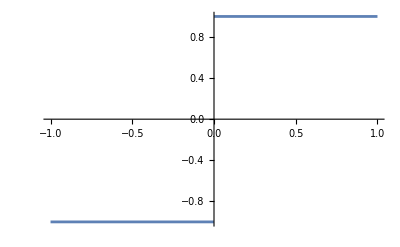

```mathematica
Plot[f[x], {x, -1, 1}]
```

Está claro que el límite de la izquierda en 0 es −1, y el límite de la derecha en 0 es 1.

```mathematica
{Limit[f[x], x -> 0, Direction -> 1], Limit[f[x], x -> 0, Direction -> -1]}
```

{-1,1}

Confirmar con límite:

```mathematica
Limit[f[x], x -> 0]
```

Indeterminate

```mathematica
Por lo tanto, el límite es inexistente.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Función de suelo

```mathematica
La función floor calcula el mayor entero menor o igual que x.
```

```mathematica
Encuentre los lugares donde no existe el límite para la función de piso en el rango de −2 a 2:
```

```mathematica
f[x_] := Floor[x]
```

Comience trazando la función:

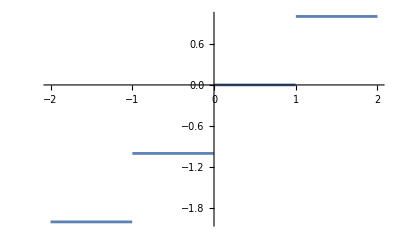

```mathematica
Plot[f[x], {x, -2, 2}]
```

Parece que el límite no existe en ninguno de los números enteros.

```mathematica
Por ejemplo, en 0 los límites izquierdo y derecho son −1 y 0 respectivamente:
```

```mathematica
{Limit[f[x], x -> 0, Direction -> 1], Limit[f[x], x -> 0, Direction -> -1]}
```

{-1,0}

Limit confirma esto en cada uno de los enteros −2, −1, 0, 1 y 2. Utilice también #, &, /@ y Range:

```mathematica
(Limit[f[x], x -> #1] & ) /@ Range[-2, 2]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

◀ prev - + prox ▶

e Guardar
d Resetear

### Teorema de compresión

```mathematica
Si f[x] es mayor que g[x] cerca de a, entonces el límite de f en a es mayor que el límite de g en a. Con esto, puedes extender a tres funciones y usar lo que se llama el teorema de la compresión: Si f[x] ≥ g[x] cerca de a, y g[x] ≥ h[x] cerca de a, y los límites de f y h en a son L, entonces el límite de g en a también es L.
```

```mathematica
Usa el teorema de compresión para encontrar el límite de la siguiente función cuando x tiende a 0:
```

```mathematica
g[x_] := x^2  Cos[1/x]
```

Dado que el coseno se encuentra estrictamente entre 1 y −1, las funciones que unen g deben ser x^2 y -x^2. Puedes ver esto en un gráfico:

```mathematica
f[x_] = x^2 ;
```

```mathematica
h[x_] = -x^2 ;
```

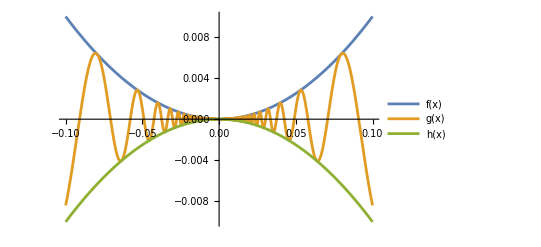

```mathematica
Plot[{f[x], g[x], h[x]}, {x, -0.1, 0.1}, PlotLegends -> "Expressions"]
```

```mathematica
Ya conoces los límites cuando x tiende a 0 para f y h, ya que son funciones polinómicas:
```

```mathematica
{Limit[g[x], x -> 0], Limit[h[x], x -> 0]}
```

{0,0}

Por lo tanto, el límite también debe ser 0 para g, como se muestra en Limit:

```mathematica
Limit[f[x], x -> 0]
```

0

◀ prev - + prox ▶

e Guardar
d Resetear

### Resumen

```mathematica
En lugar de tener que mirar las tablas para determinar los límites, las leyes de los límites dan una forma de encontrar los límites de las funciones matemáticamente.
```

```mathematica
Las leyes incluyen situaciones para sumas, diferencias, productos y cocientes.
```

```mathematica
A partir de estas leyes, se puede encontrar fácilmente el límite de cualquier polinomio.
```

Para funciones algebraicas racionales y generales, a veces es mejor intentar factorizar la función para calcular el límite.

```mathematica
En el caso de las funciones a trozos, a veces es mejor calcular los límites izquierdo y derecho de la función para calcular el límite.
```

Para una función que se encuentra entre otras dos funciones, el teorema de compresión puede ser útil al calcular el límite.

```mathematica
La siguiente lección cubrirá las funciones continuas, lo que facilitará aún más el cálculo de los límites de las funciones.
```

◀ prev - + prox ▶

e Guardar
d Resetear

### Ejercicio 1: Polinomio

Calcule el límite de la siguiente función cuando x tiende a 1:

```mathematica
f[x_] := x^6  + 3 x^2  + 9
```

#### Solución

```mathematica
Dado que f es un polinomio, puedes simplemente reemplazar 1 para obtener la respuesta:
```

```mathematica
f[1]
```

13

```mathematica
Limit está de acuerdo:
```

```mathematica
Limit[f[x], x -> 1] == 13
```

True

Aquí está su gráfico:

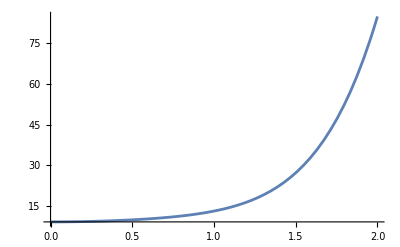

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, 0, 2}]
```

### Ejercicio 2: Límite de suma

```mathematica
Calcule el límite de la siguiente función cuando x tiende a −4:
```

```mathematica
f[x_] := 3 x + Abs[x + 4]
```

#### Solución

Usa la ley de la suma para resolver esto:

```mathematica
g[x_] := 3 x
```

```mathematica
h[x_] := Abs[x + 4]
```

Suma los límites de las dos funciones:

```mathematica
Limit[g[x], x -> -4] + Limit[h[x], x -> -4]
```

-12

```mathematica
Limit está de acuerdo:
```

```mathematica
Limit[f[x], x -> -4] == -12
```

True

Aquí está su gráfico:

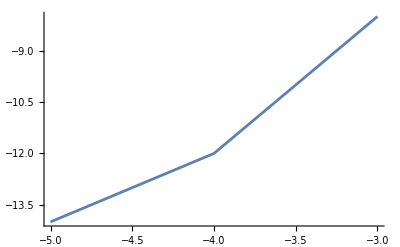

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, -5, -3}]
```

### Ejercicio 3: Límite de un producto

Calcule el límite de la siguiente función cuando x tiende a 2:

```mathematica
f[x_] := (x^4  - 5 x) (3 - Sqrt[x])
```

#### Solución

Utiliza la ley del producto, ya que es producto de dos polinomios:

```mathematica
g[x_] := x^4  - 5 x
```

```mathematica
h[x_] := 3 - Sqrt[x]
```

```mathematica
Multiplica los límites de las dos funciones:
```

```mathematica
{Limit[g[x], x -> 2] Limit[h[x], x -> 2], N[Limit[g[x], x -> 2] Limit[h[x], x -> 2]]}
```

{6 (3-√2),9.51472}

Limit está de acuerdo:

```mathematica
Limit[f[x], x -> 2] == 6 (3 - Sqrt[2])
```

True

```mathematica
Aquí está su gráfico:
```

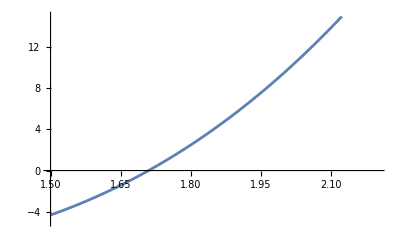

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, 1.5, 2.2}, PlotRange -> {-5, 15}, GridLines -> {{2}, {6 (3 - Sqrt[2])}}]
```

### Ejercicio 4—Límite de un cociente

Calcule el límite de la siguiente función cuando x tiende a 0:

```mathematica
f[x_] := 2 x^4  + 5/( 7 x + 9)
```

#### Solución

Esta es una función racional, así que intenta conectar 0:

```mathematica
f[0]
```

5/9

Limit está de acuerdo:

```mathematica
Limit[f[x], x -> 0] ==5/9
```

True

```mathematica
Aquí está su gráfico:
```

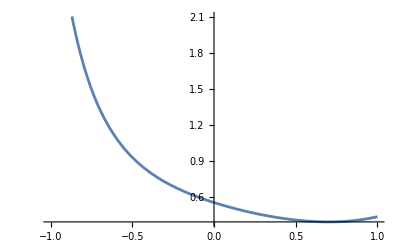

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, -1, 1}]
```

### Ejercicio 5: Otro límite de un cociente

Calcule el límite de la siguiente función cuando x tiende a 0:

```mathematica
f[x_] := Sqrt[5 + x] - Sqrt[5]/x
```

#### Solución

```mathematica
Vea si simplificarlo hace que sea más fácil lidiar con:
```

```mathematica
FullSimplify[f[x]]
```

1/(√5+√(5+x))

```mathematica
Ahora está claro que el límite debe ser 1/(2 √5):
```

Confirme con la función original:

```mathematica
Limit[f[x], x -> 0]
```

1/(2 √5)

```mathematica
Aquí está su gráfico con una línea de cuadrícula horizontal en 1/(2 √5):
```

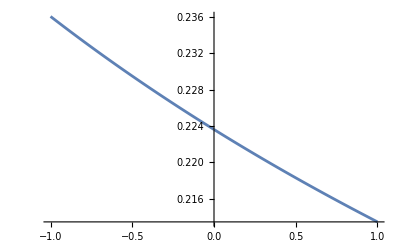

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
Plot[f[x], {x, -1, 1}, GridLines -> {None, {1/2 Sqrt[5]}}]
```

### Ejercicio 6: Teorema de compresión

Calcule el límite para la siguiente función:

```mathematica
f[x_] := x Sin[1/x]
```

#### Solución

El uso de la regla del producto no funcionará, ya que el límite no existe para Sin[1/x]:

```mathematica
Limit[Sin[1/x], x -> 0]
```

Indeterminate

Dado que el seno se encuentra entre 1 y −1, use el teorema de compresión con funciones de contorno |x| y -|x| (No puede usar x y -x porque x≥-x para x≥0, pero -x>x para x<0):

```mathematica
g[x_] := RealAbs[x]
```

```mathematica
h[x_] := -RealAbs[x]
```

El límite cuando x tiende a 0 para g y h es 0. Por lo tanto, el límite de f también debe ser 0:

```mathematica
{{Limit[g[x], x -> 0], Limit[h[x], x -> 0]}, Limit[f[x], x -> 0] == 0}
```

{{0,0},True}

```mathematica
También puedes verlo en sus gráficos:
```

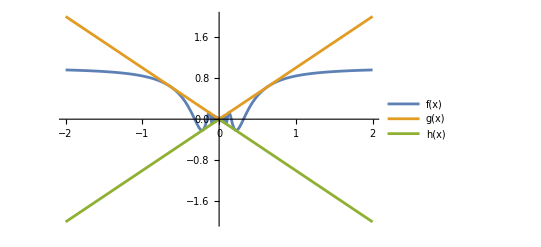

```mathematica
Plot[{f[x], g[x], h[x]}, {x, -2, 2}, PlotLegends -> "Expressions"]
```

### Ejercicio final: contracción de la longitud

```mathematica
En la teoría de la relatividad especial, la fórmula de contracción de Lorentz establece que un objeto con longitud en reposo Subíndice[L, 0] y velocidad v con respecto a un observador estacionario tiene una nueva longitud con respecto al observador dada por:
```

```mathematica
Lorentz[v_] := L0 Sqrt[1-v^2/c^2]
```

```mathematica
L0 = 1;
```

```mathematica
c = 299792458;
```

Aquí c es la velocidad de la luz en el vacío. Establezca la longitud del resto en 1.

```mathematica
¿Cuál es el límite de la longitud del objeto cuando v tiende a c?
```

#### Solución

Vea lo que sucede cuando v se acerca a c desde la izquierda:

```mathematica
Limit[Lorentz[v],v -> c, Direction -> "FromBelow"]
```

0

```mathematica
¡La longitud se reduce a cero!
```

Aquí hay un diagrama interactivo para ilustrar. El control deslizante controla la velocidad y altera la longitud del segmento de línea con respecto a un observador estacionario:

```mathematica
mmAeScienceDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mmAeScienceDB/"<>mmAeScienceDB1,"Global`"];
```

e Guardar
d Resetear

## Referencias

https : // www . wolfram - media . com/products/introduction - to - calculus/